# Fourier sine series expansion

```mathematica
Needs["FourierSeries`"]
```

```mathematica
Clear["Global`*"]
```

## Trigonometric representation

```mathematica
order=5;
```

```mathematica
f=SquareWave[{-1,1},x];
```

```mathematica
fss=FourierSinSeries[f,x,order,FourierParameters->{1,2π}]
```

(4 Sin[2 π x])/π+(4 Sin[6 π x])/(3 π)+(4 Sin[10 π x])/(5 π)

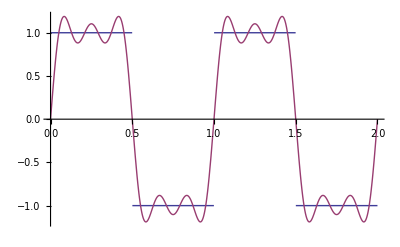

```mathematica
Plot[{f,fss},{x,0,2}]
```

### Fourier sine coefficient

```mathematica
FourierSinCoefficient[f,x,n,FourierParameters->{1,2π}]
```

(4 Sin[(n π)/2]^2)/(n π)

## Complex representation

```mathematica
fs=FourierSeries[f,x,order,FourierParameters->{1,2π}]
```

(2 ⅈ ⅇ^(-2 ⅈ π x))/π-(2 ⅈ ⅇ^(2 ⅈ π x))/π+(2 ⅈ ⅇ^(-6 ⅈ π x))/(3 π)-(2 ⅈ ⅇ^(6 ⅈ π x))/(3 π)+(2 ⅈ ⅇ^(-10 ⅈ π x))/(5 π)-(2 ⅈ ⅇ^(10 ⅈ π x))/(5 π)

```mathematica
Plot[{f,fs},{x,0,2}]
```

-Graphics-

### Fourier coefficient

```mathematica
FourierCoefficient[f,x,n,FourierParameters->{1,2π}]
```

-(ⅈ (-1)^n (-1+(-1)^n))/(n π)